```mathematica
Quit
```

```mathematica
Kin = 8*h/d^2
Kin = h
F[x_] = Piecewise[{{Kin*x,Abs[x]<d/2}}, -K*(Abs[x]-d/2)*Sign[x]]
```

(8 h)/d^2

h

Piecewise[{{h x, Abs[x]<d/2}, {-K (-d/2+Abs[x]) Sign[x], True}}]

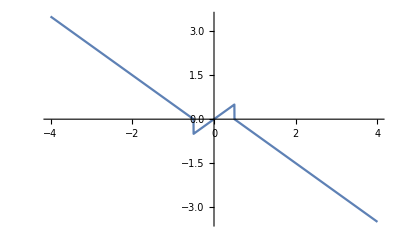

```mathematica
Plot[F[x]/.h->1/.d->1/.K->1,{x,-4,4}]
```

```mathematica
U[x_]= Assuming[{x∈Reals&& h>0&&d>0&&K>0},-Integrate[F[xd],{xd,-d/2,x}]]
```

-(Piecewise[{{1/8 (-d^2 h+4 h x^2), d-2 x≥0&&d+2 x>0&&d>0}, {1/8 (-d^2 K-4 d K x-4 K x^2), d-2 x≥0&&d+2 x<0&&d>0}, {1/8 (-d^2 K+4 d K x-4 K x^2), d-2 x<0&&d+2 x≥0&&d>0}, {0, True}}])

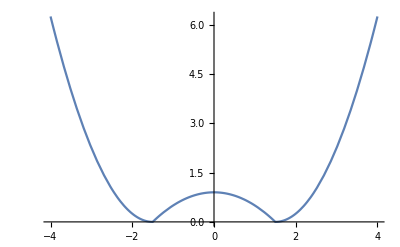

```mathematica
Plot[U[x]/.h->0.8/.d->3/.K->2,{x,-4,4}]
```

```mathematica
Quit
```